### Problem 3

```mathematica
Orthogonalize[Table[x^n,{n,0,5}],Integrate[#1 #2,{x,-1,1}]&]
```

{1/(√2),√(3/2) x,3/2 √(5/2) (-1/3+x^2),5/2 √(7/2) (-(3 x)/5+x^3),(105 (-1/5+x^4-6/7 (-1/3+x^2)))/(8 √2),63/8 √(11/2) (-(3 x)/7+x^5-10/9 (-(3 x)/5+x^3))}

### Problem 4 (Hermite Polynomials)

```mathematica
Orthogonalize[Table[x^n,{n,0,5}],Integrate[#1 #2*Exp[-x^2],{x,-Infinity,Infinity}]&]
```

{1/π^(1/4),(√2 x)/π^(1/4),(√2 (-1/2+x^2))/π^(1/4),(2 (-(3 x)/2+x^3))/(√3 π^(1/4)),(√(2/3) (-3/4+x^4-3 (-1/2+x^2)))/π^(1/4),(2 (-(15 x)/4+x^5-5 (-(3 x)/2+x^3)))/(√15 π^(1/4))}

### Problem 5

```mathematica
Involutions[0]=1;
Involutions[1]=1;
Involutions[n_]:=Involutions[n]=Involutions[n-1]+(n-1)Involutions[n-2]
```

### Problem 6 and 9

```mathematica
Valuation[n_,p_]:=Valuation[n,p]=IntegerExponent[Abs[Numerator[n]],p]-IntegerExponent[Denominator[n],p]
```

```mathematica
SetAttributes[Valuation,Listable]
```

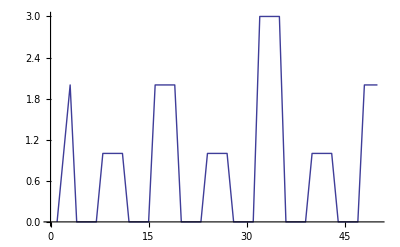

```mathematica
ListLinePlot[Table[Valuation[Involutions[n]-Floor[n/4],2],{n,1,50}]]
```

```mathematica
Table[Mod[Involutions[n],3],{n,0,50}]
```

{1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2}

### Automatic Sequence Guesser

```mathematica
PullSequence[F_,p_,coords_,values_]:=Module[{k=Length[coords],start},
start=Mod[Sum[coords[[n]]*p^(n-1),{n,1,k}],p^(k)];
Table[F[start+n*p^k],{n,0,values-1}]
]
```

```mathematica
AutomaticSequenceGuess[F_,branches_,values_,maxDepth_]:=Module[
{graph={},(*a list of coordinates paired with their corresponding outgoing edges in the form of {digit,name of target}*)
store={},(*list of sequences encountered already*)
names={},(*names of nodes corresponding to sequences seen*)
queue={{}},(*coordinates remaining to check*)
depth=0,(*length of largest coordinate -> how far down the tree goes before recursing or before the computation quits*)
coords,(*coordinates currently being checked*)
list,(*subsequence corresponding to coordinates being checked*)
name,(*name corresponding to current coordinates*)
position (*where to find the name of a node when a match is found*)
},
While[depth≤ maxDepth && queue≠{},
depth=Max[Table[Length[queue[[n]]],{n,1,Length[queue]}]]; 
coords=queue[[1]];
name=coords;
queue=Drop[queue,1];
list=PullSequence[F,branches,coords,values];
position=Position[store,list];
If[position≠{},(*thus it has been seen already*)
AppendTo[graph,{Drop[name,-1],{Last[coords],names[[position[[1,1]]]]}}],
AppendTo[store,list];
AppendTo[names,name];
queue=Join[queue,Table[Append[coords,k],{k,0,branches-1}]];
graph=If[name=={},graph,AppendTo[graph,{Drop[name,-1],{Last[name],name}}]
];
];
];
graph
]
```

```mathematica
CalcStart[F_,seq_,p_]:=If[seq=={},0,Mod[Sum[seq[[n]]*p^(n-1),{n,1,Length[seq]}],p^(Length[seq])]]
```

### Rendering the Trees

```mathematica
MakeVertexLabel[list_]:=StringJoin[ToString/@Riffle[Join[{"a"},list],"_"]]
```

```mathematica
Edges[graph_]:=DeleteDuplicates[Table[MakeVertexLabel[graph[[n,1]]]->MakeVertexLabel[graph[[n,2,2]]],{n,1,Length[graph]}]]
```

```mathematica
MakeEdgeLabels[graph_]:=Module[{position,edgelabel,from,to,pair,pairs={},label,
edgelabels={},i=0},
While[i< Length[graph],
i=i+1;
from=graph[[i,1]];
to=graph[[i,2,2]];
label=graph[[i,2,1]];
pair={from,to};
position=Position[pairs,pair];
If[position≠{},
AppendTo[edgelabels[[position[[1,1]],2]],label],
AppendTo[pairs,pair];
AppendTo[edgelabels,Labeled[MakeVertexLabel[from]->MakeVertexLabel[to],{label}]];
];
];
edgelabels
]
```

### Answers to 6 and 9

```mathematica
F[n_]:=Valuation[n^2+7,2](*for problem 9*)
```

```mathematica
G[n_]:= Valuation[Involutions[n]+Floor[n/4],2](*for problem 6*)
```

```mathematica
Graph[MakeEdgeLabels[AutomaticSequenceGuess[F,2,100,9]]]
```

-Graphics-

```mathematica
Graph[MakeEdgeLabels[AutomaticSequenceGuess[G,2,100,8]]]
```

-Graphics-

```mathematica
Manipulate[Graph[MakeEdgeLabels[AutomaticSequenceGuess[Cyclotomic[n,#]&,p,100,5]]],{n,1},{p,2}]
```